```mathematica
RemoveGlobal[];
```

ok

```mathematica
<<MultiAgent`
<<MultiAgent`
```

```mathematica
ResourceList={"Money","Labor","Water","Energy","Ferrum"};
ProdFunctions={"Linear","Min","CD","CES"};
CEpsAmount = 0.01;
CEpsPrice = 0.0001;

initHistoryVars[];
initExchange[];
initAgents[];
initMarkets[];

createProducts[
NumberOfProducts->4
];

addAgent/@ createAgents[
AgentsAmount->3,
StartMoney->0,
ProdFuncInd->1
];

addMarket/@ monoCurrencyMarkets[
SessionsInDay->1,
FirstPrice-> {5, 5}
];

goods[1,1] = 10;
goods[1,2] = 1;
goods[1,3] = 1;
goods[1,4] = 1;
goods[2,1] = 10;
goods[2,2] = 1;
goods[2,3] = 1;
goods[2,4] = 1;
goods[3,1] = 10;
goods[3,2] = 1;
goods[3,3] = 1;
goods[3,4] = 1;

agentsProds[1] = 1;
agentsProds[2] = 2;
agentsProds[3] = 3;

agentsCons[1] = 2;
agentsCons[2] = 3;
agentsCons[3] = 4;

agentsParams[1,rProduce] = {0.0,0.0,0.0,0.0};
agentsParams[2,rProduce] = {0.0,0.0,0.0,0.0};
agentsParams[3,rProduce] = {0.0,0.0,0.0,0.0};

agentsParams[1, prodFunc] = 1;
agentsParams[2, prodFunc] = 1;
agentsParams[3, prodFunc] = 1;

agentsParams[1,cLinear] = {0,0,0,2};
agentsParams[2,cLinear] = {0,0,2,0};
agentsParams[3,cLinear] = {0,2,0,0};

agentsParams[1, norm] = 0.5;
agentsParams[2, norm] = 0.5;
agentsParams[3, norm] = 0.5;

initHistory[];
```

```mathematica
?runExchange
agentGoods /@ agentsNums
productsNames
runExchange[Days->2]
```

main function that runs MAExchange

{{10,1,1,1},{10,1,1,1},{10,1,1,1}}

{Money,Labor,Water,Energy}

Assertions

```mathematica
On[Assert];
(* Off[Assert]; *)
t1 = hAgentsGoods[[#, All, All]] &/@{1,2}
Assert[
t1 == {{{10,1,1,1},{10,1,1,1},{10,1,1,1}},
	{{12,0,1,0},{(10 - 2*5*5/5.5),3,0,1},
	{(10 + 2*5*5/5.5),0,(3-2*5/5.5),0}}}
]
```

{{{10,1,1,1},{10,1,1,1},{10,1,1,1}},{{12.,0.,1.,0},{0.909091,3.,0.,1.},{19.0909,0,1.18182,0.}}}

```mathematica
t2 = hMarketsBooks[[All, #, All]] &/@ {1,2}
Assert[t2 == {{{{{{3,5.5,Ask,2,3}},{{6/4.5,4.5,Bid,1,1},{5/4.5,4.5,Bid,3,8}}}},{{{{3,4.5,Ask,3,6}},{{5/5.5,5.5,Bid,2,4},{5/5.5,5.5,Bid,2,5}}}},{{{},{{6/4.5,4.5,Bid,1,2},{5/4.5,4.5,Bid,3,7}}}}},{{{{{3,5.5,Ask,2,11}},{{6/4.5,4.5,Bid,1,9},{2.1212121212121215,4.5,Bid,3,16}}}},{{{{1.1818181818181817,4.5,Ask,3,14}},{{0.08264462809917349,5.5,Bid,2,12},{0.08264462809917349,5.5,Bid,2,13}}}},{{{},{{1.3333333333333333,4.5,Bid,1,10},{2.1212121212121215,4.5,Bid,3,15}}}}}}
]
```

{{{{{{3.,5.5,Ask,2,3}},{{1.33333,4.5,Bid,1,1},{1.11111,4.5,Bid,3,8}}}},{{{{3.,4.5,Ask,3,6}},{{0.909091,5.5,Bid,2,4},{0.909091,5.5,Bid,2,5}}}},{{{},{{1.33333,4.5,Bid,1,2},{1.11111,4.5,Bid,3,7}}}}},{{{{{3.,5.5,Ask,2,11}},{{1.33333,4.5,Bid,1,9},{2.12121,4.5,Bid,3,16}}}},{{{{1.18182,4.5,Ask,3,14}},{{0.0826446,5.5,Bid,2,12},{0.0826446,5.5,Bid,2,13}}}},{{{},{{1.33333,4.5,Bid,1,10},{2.12121,4.5,Bid,3,15}}}}}}

```mathematica
t3 = hMarketsDeals[[All, #, All]] &/@ {1,2}
Assert[t3 == {{{{}},{{{2,{-2*5*5/5.5,2*5/5.5}},{3,{2*5*5/5.5,-2*5/5.5}}}},{{}}},{{{}},{{{2,{-0.8264462809917349,0.16528925619834697}},{3,{0.826446280991735,-0.165289256198347}}}},{{}}}}
]
```

{{{{}},{{{2,{-9.09091,1.81818}},{3,{9.09091,-1.81818}}}},{{}}},{{{}},{{{2,{-0.826446,0.165289}},{3,{0.826446,-0.165289}}}},{{}}}}

```mathematica
t4 = hMarketsPrices
Assert[
t4 == {{{5},{5}},{{5},{5}},{{5},{5}}}
]
```

{{{5.},{5.}},{{5.},{5.}},{{5.},{5.}}}

Graphs

No orders on market 3day/ses: 1/1

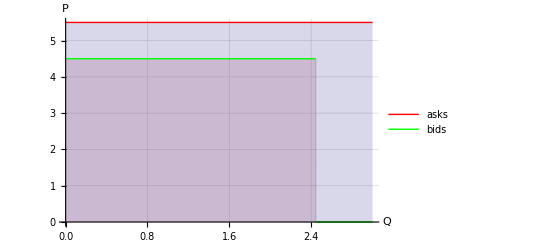
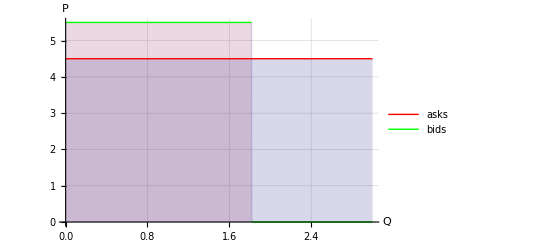
{-Graphics-,-Graphics-,Null}

No orders on market 3day/ses: 2/1

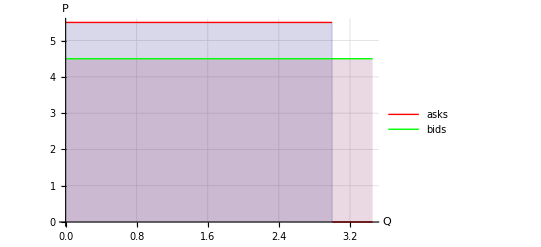
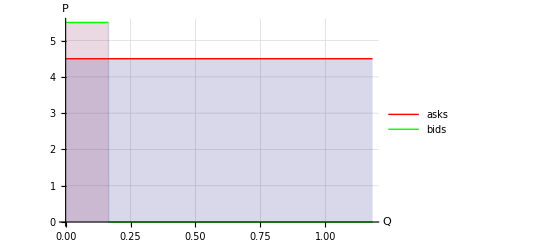
{-Graphics-,-Graphics-,Null}

```mathematica
MAEVisMarketAuction[#, 1, 1] &/@ marketsNums
MAEVisMarketAuction[#, 2, 1] &/@ marketsNums
```

```mathematica
printAgentParams/@agentsNums;
```

***** [1] Agent Parameters *****

Produces good: 1, Money

Consumed good: 2, Labor

Production function: 1

Func coefs : {0.00,0.00,0.00,2.00}

Daily regen: {0.00,0.00,0.00,0.00}

Start store: {10.00,1.00,1.00,1.00}

Consume norm: 0.50

Lambda coef: 0.49

***** [2] Agent Parameters *****

Produces good: 2, Labor

Consumed good: 3, Water

Production function: 1

Func coefs : {0.00,0.00,2.00,0.00}

Daily regen: {0.00,0.00,0.00,0.00}

Start store: {10.00,1.00,1.00,1.00}

Consume norm: 0.50

Lambda coef: 0.38

***** [3] Agent Parameters *****

Produces good: 3, Water

Consumed good: 4, Energy

Production function: 1

Func coefs : {0.00,2.00,0.00,0.00}

Daily regen: {0.00,0.00,0.00,0.00}

Start store: {10.00,1.00,1.00,1.00}

Consume norm: 0.50

Lambda coef: 0.86